一阶低通滤波器

## 1. 滤波器参数设置

采样频率

```mathematica
Fs=10000;
```

那么，采样周期为

```mathematica
Ts=1/Fs
```

1/10000

滤波器截止频率(Hz)

```mathematica
fc=10;
```

滤波器时间常数

```mathematica
Tc=1/(2 Pi fc)
```

1/(20 π)

## 2. 滤波器连续传函

滤波器传函

```mathematica
LPF=TransferFunctionModel[1/(1+Tc s),s]
N[LPF,10]
```

1/(1+s/(20 π))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11PiPi1FalseFalseFalseAutomaticNoneAutomatic

1./(1.+0.01591549431 s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s113.141592653589793238458598850781910982733.141592653589793238458598850781910982731FalseFalseFalseAutomaticNoneAutomatic

Bode图如下

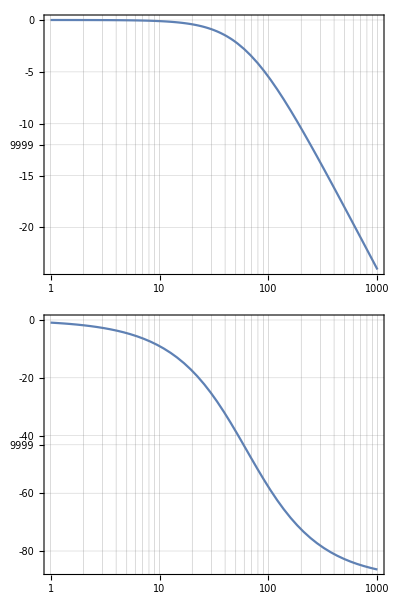

```mathematica
BodePlot[LPF,{1,1000},GridLines->Automatic,ImageSize->Medium]
```

## 3. 滤波器连续传函离散化

```mathematica
LPFz=ToDiscreteTimeModel[LPF,Ts,z,Method->{"BilinearTransform"}]
N[LPFz,10]
```

(π (1+z))/(-1000+π+1000 z+π z)1/10000TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z1110000100001FalseFalseFalseAutomaticNoneAutomatic

(3.14159265 (1.+z))/(-996.8584073+1003.141593 z)0.0001TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z1131415.926535897932384626410000.1FalseFalseFalseAutomaticNoneAutomatic

离散传函的bode图如下

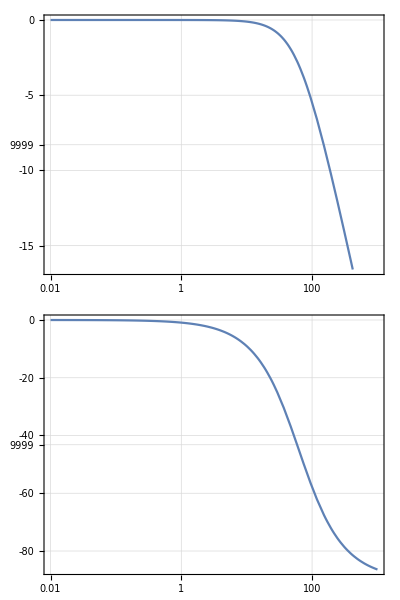

```mathematica
BodePlot[LPFz,{0.01,1000},GridLines->Automatic,ImageSize->Medium]
```

传函化简

```mathematica
N[TransferFunctionCancel[TransferFunctionExpand[LPFz]],10]
```

(0.00313175396 (1.+z))/(-0.9937364921+z)0.0001TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z113.141592653589793238458598850781910982731003.14159265358979323851FalseFalseFalseAutomaticNoneAutomatic